```mathematica
play[J_,d1_,d2_]:=ConjugateTranspose[J].(KroneckerProduct[d1,d2].(J.{1,0,0,0}))
```

```mathematica
aliceMove = (su2[x1,y1,z1])//FullSimplify;
bobsMove = (su2[x2,y2,z2])//FullSimplify;
```

```mathematica
fullPlayTrig = ( ( play[JtrigForm[a,b,γ],aliceMove,bobsMove]))/.Conjugate->myFunc;
```

```mathematica
fullPlayExp =( ( play[J[a,b,γ],aliceMove,bobsMove])/.Conjugate->myFunc);
```

```mathematica
fptSimp = fullPlayTrig//FullSimplify;
```

```mathematica
fpeSimp = fullPlayExp//FullSimplify;
```

```mathematica
fptSimp
```

{Cos[z1/2] (Cos[z2/2]-ⅈ Cos[γ] Sin[z2/2] (Cos[x2] Cos[a γ]-Cos[y2] Sin[x2] Sin[a γ]))+Sin[z1/2] (Cos[x1] (Cos[b γ] (-ⅈ Cos[z2/2] Cos[γ]+Sin[z2/2] (-Cos[x2] Cos[a γ]+Cos[y2] Sin[x2] Sin[a γ]))+Sin[x2] Sin[y2] Sin[z2/2] Sin[γ] Sin[b γ])+Sin[x1] (Sin[z2/2] Sin[γ] (Cos[y2] Cos[a γ] Sin[x2] Sin[y1]+Cos[y1] Cos[b γ] Sin[x2] Sin[y2]+Cos[x2] Sin[y1] Sin[a γ])+Cos[y1] (ⅈ Cos[z2/2] Cos[γ]+Sin[z2/2] (Cos[x2] Cos[a γ]-Cos[y2] Sin[x2] Sin[a γ])) Sin[b γ])),Cos[z1/2] Sin[z2/2] (Sin[x2] Sin[y2]-ⅈ Cos[x2] Cos[γ] Sin[a γ])+Sin[z1/2] (Cos[x1] (Cos[b γ] Sin[z2/2] (-ⅈ Cos[γ] Sin[x2] Sin[y2]-Cos[x2] Sin[a γ])-Cos[z2/2] Sin[γ] Sin[b γ])+Sin[x1] (-((Cos[y1] Cos[z2/2] Cos[b γ]+Cos[x2] Cos[a γ] Sin[y1] Sin[z2/2]) Sin[γ])+Cos[y1] Sin[z2/2] (ⅈ Cos[γ] Sin[x2] Sin[y2]+Cos[x2] Sin[a γ]) Sin[b γ]))+Cos[y2] Sin[x2] Sin[z2/2] (-ⅈ Cos[z1/2] Cos[γ] Cos[a γ]+Sin[z1/2] (Sin[x1] Sin[y1] Sin[γ] Sin[a γ]+Cos[a γ] (-Cos[x1] Cos[b γ]+Cos[y1] Sin[x1] Sin[b γ]))),Cos[z2/2] Sin[z1/2] (Sin[x1] Sin[y1]-ⅈ Cos[x1] Cos[γ] Sin[b γ])+Cos[y1] Sin[x1] Sin[z1/2] (-ⅈ Cos[z2/2] Cos[γ] Cos[b γ]+Sin[z2/2] (-Cos[x2] Cos[a γ] Cos[b γ]+Cos[y2] Cos[b γ] Sin[x2] Sin[a γ]+Sin[x2] Sin[y2] Sin[γ] Sin[b γ]))+Sin[z2/2] (Cos[x2] (-Cos[z1/2] Sin[γ] Sin[a γ]+Cos[a γ] Sin[z1/2] (-ⅈ Cos[γ] Sin[x1] Sin[y1]-Cos[x1] Sin[b γ]))+Sin[x2] (-Cos[x1] Cos[b γ] Sin[y2] Sin[z1/2] Sin[γ]+Cos[y2] (-Cos[z1/2] Cos[a γ] Sin[γ]+Sin[z1/2] Sin[a γ] (ⅈ Cos[γ] Sin[x1] Sin[y1]+Cos[x1] Sin[b γ])))),Sin[x1] Sin[x2] Sin[y1] Sin[y2] Sin[z1/2] Sin[z2/2]+Cos[x1] Cos[z2/2] Cos[(b γ)/2]^2 Sin[z1/2] Sin[γ]+Cos[x2] Cos[z1/2] Cos[(a γ)/2]^2 Sin[z2/2] Sin[γ]-Cos[x2] Cos[z1/2] Sin[z2/2] Sin[γ] Sin[(a γ)/2]^2-ⅈ Cos[x2] Cos[γ/2]^2 Sin[x1] Sin[y1] Sin[z1/2] Sin[z2/2] Sin[a γ]+ⅈ Cos[x2] Sin[x1] Sin[y1] Sin[z1/2] Sin[z2/2] Sin[γ/2]^2 Sin[a γ]-Cos[x1] Cos[z2/2] Sin[z1/2] Sin[γ] Sin[(b γ)/2]^2-Cos[x1] Sin[z1/2] Sin[z2/2] (ⅈ Cos[γ] Sin[x2] Sin[y2]+Cos[x2] Sin[a γ]) Sin[b γ]+Cos[y1] Sin[x1] Sin[z1/2] (-Cos[b γ] Sin[z2/2] (Cos[y2] Cos[a γ] Sin[x2]+ⅈ Cos[γ] Sin[x2] Sin[y2]+Cos[x2] Sin[a γ])-Cos[z2/2] Sin[γ] Sin[b γ])+Cos[y2] Sin[x2] Sin[z2/2] (-Cos[z1/2] Sin[γ] Sin[a γ]+Cos[a γ] Sin[z1/2] (-ⅈ Cos[γ] Sin[x1] Sin[y1]-Cos[x1] Sin[b γ]))}

```mathematica
ascore = alicesScore[fptSimp]//ComplexExpand;
```

```mathematica
totalChanged=0;
n=Length[ascore];

resultList=Monitor[Table[Module[{s=Simplify[ascore[[i]]]},If[s=!=ascore[[i]],totalChanged++];
s],{i,n}],ProgressIndicator[i/n,{0,1},ImageSize->200]];

Print["Total changed: ",totalChanged," of ",n];
Print["Final total length: ",Length[resultList], " where previous length was " ,Length[ascore], " and initial length was ", Length[alicesScore[fptSimp]//ComplexExpand]];

ascore = Total[resultList];
```

Total changed: 0 of 82

Final total length: 82 where previous length was 82 and initial length was 165

```mathematica
totalChanged=0;
n=Length[ascore];

resultList=Monitor[
Table[
Module[{s=Simplify[ascore[[i]]+ascore[[i+1]]]},
If[s=!=ascore[[i]]+ascore[[i+1]],totalChanged++];
s
],{i,1,n-1,2}],

ProgressIndicator[i,{0,n-1},ImageSize->200]];

If[OddQ[n],resultList = Append[resultList,ascore[[n]]]];

Print["Total changed: ",totalChanged," of ",n];
Print["Final total length: ",Length[resultList//Total], " where previous length was " ,Length[ascore], " and initial length was ", Length[alicesScore[fptSimp]//ComplexExpand]];
ascore = Total[resultList];
```

```mathematica
bscore =ascore/.{a->b,b->a,x1->x2,y1->y2,z1->z2,x2->x1,y2->y1,z2->z1};
```

## Choose a specific Game

```mathematica
params = {0,0,Pi/2};
ascoreSpecific = ascore/.{a->params[[1]],b->params[[2]],γ->params[[3]]};
bscoreSpecific =ascoreSpecific/.{a->b,b->a,x1->x2,y1->y2,z1->z2,x2->x1,y2->y1,z2->z1};
```

```mathematica
totalChanged=0;
n=Length[ascoreSpecific];

resultList=Monitor[Table[Module[{s=Simplify[ascoreSpecific[[i]]]},If[s=!=ascoreSpecific[[i]],totalChanged++];
s],{i,n}],ProgressIndicator[i/n,{0,1},ImageSize->200]];

Print["Total changed: ",totalChanged," of ",n];
Print["Final total length: ",Length[resultList], " where previous length was " ,Length[ascoreSpecific], " and initial length was ", Length[alicesScore[fptSimp]//ComplexExpand]];

ascoreSpecific = Total[resultList];
```

Total changed: 3 of 7

Final total length: 7 where previous length was 7 and initial length was 165

```mathematica
totalChanged=0;
n=Length[ascoreSpecific];

resultList=Monitor[
Table[
Module[{s=Simplify[ascoreSpecific[[i]]+ascoreSpecific[[i+1]]]},
If[s=!=ascoreSpecific[[i]]+ascoreSpecific[[i+1]],totalChanged++];
s
],{i,1,n-1,2}],

ProgressIndicator[i,{0,n-1},ImageSize->200]];

If[OddQ[n],resultList = Append[resultList,ascore[[n]]]];

Print["Total changed: ",totalChanged," of ",n];
Print["Final total length: ",Length[resultList//Total], " where previous length was " ,Length[ascoreSpecific], " and initial length was ", Length[alicesScore[fptSimp]//ComplexExpand]];
ascoreSpecific = Total[resultList];
```

$Aborted

Total changed: 4 of 12

Final total length: 12 where previous length was 12 and initial length was 165

```mathematica
n
```

12

```mathematica
ascoreSpecific
```

Cos[x1]^2 Cos[z2/2]^2 Sin[z1/2]^2+Cos[z2/2]^2 (3 Cos[z1/2]^2+5 Sin[x1]^2 Sin[y1]^2 Sin[z1/2]^2)+Cos[x2]^2 Cos[z1/2]^2 Sin[z2/2]^2+Cos[y1]^2 Sin[x1]^2 (5 Cos[x2]^2+Cos[y2]^2 Sin[x2]^2) Sin[z1/2]^2 Sin[z2/2]^2+Sin[x2]^2 (Sin[y2] (6 Cos[y1] Cos[y2] Sin[x1]^2 Sin[y1]+5 Cos[x1]^2 Sin[y2]) Sin[z1/2]^2+Cos[y2]^2 (5 Cos[z1/2]^2+3 Sin[x1]^2 Sin[y1]^2 Sin[z1/2]^2)) Sin[z2/2]^2+Sin[x2]^2 Sin[y2] (3 Cos[y1]^2 Sin[x1]^2 Sin[y2] Sin[z1/2]^2+5 Cos[x1] Cos[y2] Sin[z1]) Sin[z2/2]^2+(3 Cos[x1]^2 Cos[x2]^2 Sin[z1/2]^2-6 Cos[x1] Cos[x2] Cos[y2] Sin[x1] Sin[x2] Sin[y1] Sin[z1/2]^2+Sin[x1]^2 Sin[x2]^2 Sin[y1]^2 Sin[y2]^2 Sin[z1/2]^2+Cos[y1] Sin[2 x2] (Sin[2 x1] Sin[y2] Sin[z1/2]^2+2 Cos[y2] Sin[x1] Sin[z1])) Sin[z2/2]^2+1/2 Cos[x1] Cos[x2] Sin[z1] Sin[z2]-1/2 Cos[x2] (5 Sin[x1]^2 Sin[2 y1] Sin[z1/2]^2+3 Cos[x1] Sin[z1]) Sin[z2]-1/2 Sin[x2] (4 Sin[2 x1] Sin[y1] Sin[y2] Sin[z1/2]^2+Sin[x1] (2 Cos[y2] Sin[y1]-3 Cos[y1] Sin[y2]) Sin[z1]) Sin[z2]+Sin[x1] Sin[x2] (Cos[x2] Sin[y1] Sin[y2] Sin[z1] Sin[z2/2]^2-Cos[y1] Cos[y2] Sin[z1/2]^2 (2 Sin[x1] Sin[x2] Sin[y1] Sin[y2] Sin[z2/2]^2+Cos[x1] Sin[z2]))

```mathematica
ascoreFunc[a_,b_,γ_,x1_,y1_,z1_,x2_,y2_,z2_] = ascoreSpecific;
bscoreFunc[a_,b_,γ_,x1_,y1_,z1_,x2_,y2_,z2_] =  bscoreSpecific;
```

```mathematica
ascoreSpecific
```

Cos[z2/2]^2 (3 Cos[z1/2]^2+5 Sin[x1]^2 Sin[y1]^2 Sin[z1/2]^2)+Cos[y1]^2 Sin[x1]^2 (5 Cos[x2]^2+Cos[y2]^2 Sin[x2]^2) Sin[z1/2]^2 Sin[z2/2]^2+1/4 (4 (-6 Cos[x1] Cos[x2] Cos[y2] Sin[x1] Sin[x2] Sin[y1]+Cos[y1] Sin[2 x1] Sin[2 x2] Sin[y2]) Sin[z1/2]^2+4 (3 Cos[x1]^2 Cos[x2]^2 Sin[z1/2]^2+Sin[x1]^2 Sin[x2]^2 Sin[y1]^2 Sin[y2]^2 Sin[z1/2]^2)+8 Cos[y1] Cos[y2] Sin[x1] Sin[2 x2] Sin[z1]) Sin[z2/2]^2-1/2 Cos[x2] (5 Sin[x1]^2 Sin[2 y1] Sin[z1/2]^2+3 Cos[x1] Sin[z1]) Sin[z2]+1/2 (2 (Cos[x1]^2 Cos[z2/2]^2 Sin[z1/2]^2+Cos[x2]^2 Cos[z1/2]^2 Sin[z2/2]^2+Sin[x2]^2 Sin[y2] (3 Cos[y1]^2 Sin[x1]^2 Sin[y2] Sin[z1/2]^2+5 Cos[x1] Cos[y2] Sin[z1]) Sin[z2/2]^2)+Cos[x1] Cos[x2] Sin[z1] Sin[z2])+1/4 Sin[x2] (4 Sin[x2] (Sin[y2] (6 Cos[y1] Cos[y2] Sin[x1]^2 Sin[y1]+5 Cos[x1]^2 Sin[y2]) Sin[z1/2]^2+Cos[y2]^2 (5 Cos[z1/2]^2+3 Sin[x1]^2 Sin[y1]^2 Sin[z1/2]^2)) Sin[z2/2]^2-(8 Sin[2 x1] Sin[y1] Sin[y2] Sin[z1/2]^2+2 Sin[x1] (2 Cos[y2] Sin[y1]-3 Cos[y1] Sin[y2]) Sin[z1]) Sin[z2])+Sin[x1] Sin[x2] (Cos[x2] Sin[y1] Sin[y2] Sin[z1] Sin[z2/2]^2-Cos[y1] Cos[y2] Sin[z1/2]^2 (2 Sin[x1] Sin[x2] Sin[y1] Sin[y2] Sin[z2/2]^2+Cos[x1] Sin[z2]))

```mathematica
aliceBestResponse[bobsMove_]:=Module[{a,b,γ,x2,y2,z2,aScoreGivenBob},
{x2,y2,z2} = bobsMove;
aScoreGivenBob[x1_,y1_,z1_] := ascoreFunc[a,b,γ,x1,y1,z1,x2,y2,z2];
Mod[NArgMax[aScoreGivenBob[x1,y1,z1],{x1,y1,z1}],{Pi,Pi,2Pi}]
]
```

```mathematica
aliceBestResponse[{0,2,1}]
```

{1.5708,2.0708,3.14159}

```mathematica
bscoreFunc[0,0,1,0,0,0,0,0,0]
```

3

```mathematica
Manipulate[{MatrixForm[Chop[aliceBestResponse[{x2,y2,z2}],10^-5]],Chop[MatrixForm[{x2,y2,z2}],10^-5]},{x2,0,Pi,Pi/1000},{y2,0,Pi,Pi/1000},{z2,0,2Pi,2 Pi/1000}]
```

```mathematica
Manipulate[Module[{x1,y1,z1,a,b,γ},
{x1,y1,z1}=Chop[aliceBestResponse[{x2,y2,z2}],10^-5];
{a,b,γ} = gameParams;
{MatrixForm[Chop[{x1,y1,z1},10^-5]],Chop[MatrixForm[{x2,y2,z2}],10^-5],ascoreFunc[a,b,γ,x1,y1,z1,x2,y2,z2]//N}

]

,{x2,0,Pi},{y2,0,Pi},{z2,0,2Pi}]
```

```mathematica
Manipulate[Module[{a,b,γ},
{a,b,γ} = params;
DensityPlot3D[ascoreFunc[a,b,γ,x1,y1,z1,x2,y2,z2],{x1,0,Pi},{y1,0,Pi},{z1,0,2Pi},PlotRange->{0,5}]

]

,{{x2,1.1781},0,Pi},{{y2,2.00119},0,Pi},{{z2,1.91637},0,2Pi}];
```

```mathematica
ParallelTable[i,{i,100}]
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
frames = ParallelTable[Module[{a,b,γ},
{a,b,γ} = params;
DensityPlot3D[ascoreFunc[a,b,γ,x1,y1,z1,1.1781,2.00119,z2],{x1,0,Pi},{y1,0,Pi},{z1,0,2Pi},PlotRange->{0,5}]

]

,{z2,0,2Pi,2 Pi/20}];
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

```mathematica
ContourPlot3D[ascoreFunc[params[[1]],params[[2]],params[[3]],x1,y1,z1,0,0,Pi/2],{x1,0,Pi},{y1,0,Pi},{z1,0,2Pi},PlotRange->{0,5}]
```

$Aborted

```mathematica
Export["animation.gif",frames,"DisplayDurations"->0.2];
```

```mathematica
ListAnimate[frames]
```

```mathematica
Mod[{3,3,3},{2,3,4}]
```

{1,0,3}

```mathematica
Manipulate[Plot[Flatten[su2[x,y,z]]//ReIm,{z,0,2Pi},PlotRange-> {-1,1}],{y,0,Pi},{x,0,Pi}]
```

```mathematica
Manipulate[Plot[Flatten[su2[x,y,z]]//ReIm,{y,0,Pi},PlotRange-> {-1,1}],{z,0,2Pi},{x,0,Pi}]
```

```mathematica
varspecs = {
{a,0,100},
{x1,0,Pi},
{y1,0,Pi},
{z1,0,Pi},
{x2,0,Pi},
{y2,0,Pi},
{z2,0,Pi}};
Manipulate[
Plot[{ascoreFunc[a,a,γ,x1,y1,z1,x2,y2,z2],bscoreFunc[a,a,γ,x1,y1,z1,x2,y2,z2]},{γ,0,Pi/2},PlotRange->{0,5}],Evaluate[Sequence@@varspecs]]
```

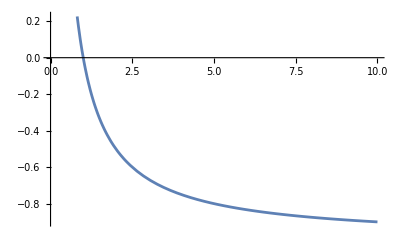

```mathematica
Plot[1/a-1,{a,0,10}]
```

```mathematica
varspecs = {
{a,0,100},
{x1,0,Pi},
{y1,0,Pi},
{z1,0,Pi},
{x2,0,Pi},
{y2,0,Pi},
{z2,0,Pi}};
Manipulate[
Plot[{finalState[a,a,γ,x1,y1,z1,x2,y2,z2]//Re,finalState[a,a,γ,x1,y1,z1,x2,y2,z2]//Im},{γ,0,Pi/2},PlotRange->{-1,1}],Evaluate[Sequence@@varspecs]]
```

```mathematica
fullPlay2/.Conjugate->myFunc
```

{ⅇ^(-1/2 ⅈ a b γ) (ⅈ Cos[(a γ)/2] Cos[(b γ)/2] Sin[γ/2]+Cos[γ/2] Sin[(a γ)/2] Sin[(b γ)/2]) (-ⅈ ⅇ^(1/2 ⅈ a b γ) Sin[x2] (-ⅈ Cos[y2]+Sin[y2]) (Cos[z1/2]+ⅈ Cos[x1] Sin[z1/2]) Sin[z2/2] (Cos[(b γ)/2] Sin[γ/2] Sin[(a γ)/2]-ⅈ Cos[γ/2] Cos[(a γ)/2] Sin[(b γ)/2])-ⅇ^(1/2 ⅈ a b γ) Sin[x1] (-ⅈ Cos[y1]+Sin[y1]) Sin[z1/2] (Cos[z2/2]+ⅈ Cos[x2] Sin[z2/2]) (Cos[γ/2] Cos[(b γ)/2] Sin[(a γ)/2]+ⅈ Cos[(a γ)/2] Sin[γ/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) (Cos[z1/2]+ⅈ Cos[x1] Sin[z1/2]) (Cos[z2/2]+ⅈ Cos[x2] Sin[z2/2]) (-ⅈ Cos[(a γ)/2] Cos[(b γ)/2] Sin[γ/2]+Cos[γ/2] Sin[(a γ)/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) Sin[x1] Sin[x2] (-ⅈ Cos[y1]+Sin[y1]) (-ⅈ Cos[y2]+Sin[y2]) Sin[z1/2] Sin[z2/2] (Cos[γ/2] Cos[(a γ)/2] Cos[(b γ)/2]-ⅈ Sin[γ/2] Sin[(a γ)/2] Sin[(b γ)/2]))-ⅇ^(-1/2 ⅈ a b γ) (Cos[γ/2] Cos[(b γ)/2] Sin[(a γ)/2]-ⅈ Cos[(a γ)/2] Sin[γ/2] Sin[(b γ)/2]) (-ⅈ ⅇ^(1/2 ⅈ a b γ) Sin[x1] Sin[x2] (-ⅈ Cos[y1]-Sin[y1]) (-ⅈ Cos[y2]+Sin[y2]) Sin[z1/2] Sin[z2/2] (Cos[(b γ)/2] Sin[γ/2] Sin[(a γ)/2]-ⅈ Cos[γ/2] Cos[(a γ)/2] Sin[(b γ)/2])-ⅇ^(1/2 ⅈ a b γ) (Cos[z1/2]-ⅈ Cos[x1] Sin[z1/2]) (Cos[z2/2]+ⅈ Cos[x2] Sin[z2/2]) (Cos[γ/2] Cos[(b γ)/2] Sin[(a γ)/2]+ⅈ Cos[(a γ)/2] Sin[γ/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) Sin[x1] (-ⅈ Cos[y1]-Sin[y1]) Sin[z1/2] (Cos[z2/2]+ⅈ Cos[x2] Sin[z2/2]) (-ⅈ Cos[(a γ)/2] Cos[(b γ)/2] Sin[γ/2]+Cos[γ/2] Sin[(a γ)/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) Sin[x2] (-ⅈ Cos[y2]+Sin[y2]) (Cos[z1/2]-ⅈ Cos[x1] Sin[z1/2]) Sin[z2/2] (Cos[γ/2] Cos[(a γ)/2] Cos[(b γ)/2]-ⅈ Sin[γ/2] Sin[(a γ)/2] Sin[(b γ)/2]))+ⅈ ⅇ^(-1/2 ⅈ a b γ) (Cos[(b γ)/2] Sin[γ/2] Sin[(a γ)/2]+ⅈ Cos[γ/2] Cos[(a γ)/2] Sin[(b γ)/2]) (-ⅈ ⅇ^(1/2 ⅈ a b γ) (Cos[z1/2]+ⅈ Cos[x1] Sin[z1/2]) (Cos[z2/2]-ⅈ Cos[x2] Sin[z2/2]) (Cos[(b γ)/2] Sin[γ/2] Sin[(a γ)/2]-ⅈ Cos[γ/2] Cos[(a γ)/2] Sin[(b γ)/2])-ⅇ^(1/2 ⅈ a b γ) Sin[x1] Sin[x2] (-ⅈ Cos[y1]+Sin[y1]) (-ⅈ Cos[y2]-Sin[y2]) Sin[z1/2] Sin[z2/2] (Cos[γ/2] Cos[(b γ)/2] Sin[(a γ)/2]+ⅈ Cos[(a γ)/2] Sin[γ/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) Sin[x2] (-ⅈ Cos[y2]-Sin[y2]) (Cos[z1/2]+ⅈ Cos[x1] Sin[z1/2]) Sin[z2/2] (-ⅈ Cos[(a γ)/2] Cos[(b γ)/2] Sin[γ/2]+Cos[γ/2] Sin[(a γ)/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) Sin[x1] (-ⅈ Cos[y1]+Sin[y1]) Sin[z1/2] (Cos[z2/2]-ⅈ Cos[x2] Sin[z2/2]) (Cos[γ/2] Cos[(a γ)/2] Cos[(b γ)/2]-ⅈ Sin[γ/2] Sin[(a γ)/2] Sin[(b γ)/2]))+ⅇ^(-1/2 ⅈ a b γ) (Cos[γ/2] Cos[(a γ)/2] Cos[(b γ)/2]+ⅈ Sin[γ/2] Sin[(a γ)/2] Sin[(b γ)/2]) (-ⅈ ⅇ^(1/2 ⅈ a b γ) Sin[x1] (-ⅈ Cos[y1]-Sin[y1]) Sin[z1/2] (Cos[z2/2]-ⅈ Cos[x2] Sin[z2/2]) (Cos[(b γ)/2] Sin[γ/2] Sin[(a γ)/2]-ⅈ Cos[γ/2] Cos[(a γ)/2] Sin[(b γ)/2])-ⅇ^(1/2 ⅈ a b γ) Sin[x2] (-ⅈ Cos[y2]-Sin[y2]) (Cos[z1/2]-ⅈ Cos[x1] Sin[z1/2]) Sin[z2/2] (Cos[γ/2] Cos[(b γ)/2] Sin[(a γ)/2]+ⅈ Cos[(a γ)/2] Sin[γ/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) Sin[x1] Sin[x2] (-ⅈ Cos[y1]-Sin[y1]) (-ⅈ Cos[y2]-Sin[y2]) Sin[z1/2] Sin[z2/2] (-ⅈ Cos[(a γ)/2] Cos[(b γ)/2] Sin[γ/2]+Cos[γ/2] Sin[(a γ)/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) (Cos[z1/2]-ⅈ Cos[x1] Sin[z1/2]) (Cos[z2/2]-ⅈ Cos[x2] Sin[z2/2]) (Cos[γ/2] Cos[(a γ)/2] Cos[(b γ)/2]-ⅈ Sin[γ/2] Sin[(a γ)/2] Sin[(b γ)/2])),ⅈ ⅇ^(-1/2 ⅈ a b γ) (Cos[(b γ)/2] Sin[γ/2] Sin[(a γ)/2]+ⅈ Cos[γ/2] Cos[(a γ)/2] Sin[(b γ)/2]) (-ⅈ ⅇ^(1/2 ⅈ a b γ) Sin[x2] (-ⅈ Cos[y2]+Sin[y2]) (Cos[z1/2]+ⅈ Cos[x1] Sin[z1/2]) Sin[z2/2] (Cos[(b γ)/2] Sin[γ/2] Sin[(a γ)/2]-ⅈ Cos[γ/2] Cos[(a γ)/2] Sin[(b γ)/2])-ⅇ^(1/2 ⅈ a b γ) Sin[x1] (-ⅈ Cos[y1]+Sin[y1]) Sin[z1/2] (Cos[z2/2]+ⅈ Cos[x2] Sin[z2/2]) (Cos[γ/2] Cos[(b γ)/2] Sin[(a γ)/2]+ⅈ Cos[(a γ)/2] Sin[γ/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) (Cos[z1/2]+ⅈ Cos[x1] Sin[z1/2]) (Cos[z2/2]+ⅈ Cos[x2] Sin[z2/2]) (-ⅈ Cos[(a γ)/2] Cos[(b γ)/2] Sin[γ/2]+Cos[γ/2] Sin[(a γ)/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) Sin[x1] Sin[x2] (-ⅈ Cos[y1]+Sin[y1]) (-ⅈ Cos[y2]+Sin[y2]) Sin[z1/2] Sin[z2/2] (Cos[γ/2] Cos[(a γ)/2] Cos[(b γ)/2]-ⅈ Sin[γ/2] Sin[(a γ)/2] Sin[(b γ)/2]))+ⅇ^(-1/2 ⅈ a b γ) (Cos[γ/2] Cos[(a γ)/2] Cos[(b γ)/2]+ⅈ Sin[γ/2] Sin[(a γ)/2] Sin[(b γ)/2]) (-ⅈ ⅇ^(1/2 ⅈ a b γ) Sin[x1] Sin[x2] (-ⅈ Cos[y1]-Sin[y1]) (-ⅈ Cos[y2]+Sin[y2]) Sin[z1/2] Sin[z2/2] (Cos[(b γ)/2] Sin[γ/2] Sin[(a γ)/2]-ⅈ Cos[γ/2] Cos[(a γ)/2] Sin[(b γ)/2])-ⅇ^(1/2 ⅈ a b γ) (Cos[z1/2]-ⅈ Cos[x1] Sin[z1/2]) (Cos[z2/2]+ⅈ Cos[x2] Sin[z2/2]) (Cos[γ/2] Cos[(b γ)/2] Sin[(a γ)/2]+ⅈ Cos[(a γ)/2] Sin[γ/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) Sin[x1] (-ⅈ Cos[y1]-Sin[y1]) Sin[z1/2] (Cos[z2/2]+ⅈ Cos[x2] Sin[z2/2]) (-ⅈ Cos[(a γ)/2] Cos[(b γ)/2] Sin[γ/2]+Cos[γ/2] Sin[(a γ)/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) Sin[x2] (-ⅈ Cos[y2]+Sin[y2]) (Cos[z1/2]-ⅈ Cos[x1] Sin[z1/2]) Sin[z2/2] (Cos[γ/2] Cos[(a γ)/2] Cos[(b γ)/2]-ⅈ Sin[γ/2] Sin[(a γ)/2] Sin[(b γ)/2]))-ⅈ ⅇ^(-1/2 ⅈ a b γ) (Cos[(a γ)/2] Cos[(b γ)/2] Sin[γ/2]-ⅈ Cos[γ/2] Sin[(a γ)/2] Sin[(b γ)/2]) (-ⅈ ⅇ^(1/2 ⅈ a b γ) (Cos[z1/2]+ⅈ Cos[x1] Sin[z1/2]) (Cos[z2/2]-ⅈ Cos[x2] Sin[z2/2]) (Cos[(b γ)/2] Sin[γ/2] Sin[(a γ)/2]-ⅈ Cos[γ/2] Cos[(a γ)/2] Sin[(b γ)/2])-ⅇ^(1/2 ⅈ a b γ) Sin[x1] Sin[x2] (-ⅈ Cos[y1]+Sin[y1]) (-ⅈ Cos[y2]-Sin[y2]) Sin[z1/2] Sin[z2/2] (Cos[γ/2] Cos[(b γ)/2] Sin[(a γ)/2]+ⅈ Cos[(a γ)/2] Sin[γ/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) Sin[x2] (-ⅈ Cos[y2]-Sin[y2]) (Cos[z1/2]+ⅈ Cos[x1] Sin[z1/2]) Sin[z2/2] (-ⅈ Cos[(a γ)/2] Cos[(b γ)/2] Sin[γ/2]+Cos[γ/2] Sin[(a γ)/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) Sin[x1] (-ⅈ Cos[y1]+Sin[y1]) Sin[z1/2] (Cos[z2/2]-ⅈ Cos[x2] Sin[z2/2]) (Cos[γ/2] Cos[(a γ)/2] Cos[(b γ)/2]-ⅈ Sin[γ/2] Sin[(a γ)/2] Sin[(b γ)/2]))+ⅇ^(-1/2 ⅈ a b γ) (Cos[γ/2] Cos[(b γ)/2] Sin[(a γ)/2]-ⅈ Cos[(a γ)/2] Sin[γ/2] Sin[(b γ)/2]) (-ⅈ ⅇ^(1/2 ⅈ a b γ) Sin[x1] (-ⅈ Cos[y1]-Sin[y1]) Sin[z1/2] (Cos[z2/2]-ⅈ Cos[x2] Sin[z2/2]) (Cos[(b γ)/2] Sin[γ/2] Sin[(a γ)/2]-ⅈ Cos[γ/2] Cos[(a γ)/2] Sin[(b γ)/2])-ⅇ^(1/2 ⅈ a b γ) Sin[x2] (-ⅈ Cos[y2]-Sin[y2]) (Cos[z1/2]-ⅈ Cos[x1] Sin[z1/2]) Sin[z2/2] (Cos[γ/2] Cos[(b γ)/2] Sin[(a γ)/2]+ⅈ Cos[(a γ)/2] Sin[γ/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) Sin[x1] Sin[x2] (-ⅈ Cos[y1]-Sin[y1]) (-ⅈ Cos[y2]-Sin[y2]) Sin[z1/2] Sin[z2/2] (-ⅈ Cos[(a γ)/2] Cos[(b γ)/2] Sin[γ/2]+Cos[γ/2] Sin[(a γ)/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) (Cos[z1/2]-ⅈ Cos[x1] Sin[z1/2]) (Cos[z2/2]-ⅈ Cos[x2] Sin[z2/2]) (Cos[γ/2] Cos[(a γ)/2] Cos[(b γ)/2]-ⅈ Sin[γ/2] Sin[(a γ)/2] Sin[(b γ)/2])),-ⅇ^(-1/2 ⅈ a b γ) (Cos[γ/2] Cos[(b γ)/2] Sin[(a γ)/2]-ⅈ Cos[(a γ)/2] Sin[γ/2] Sin[(b γ)/2]) (-ⅈ ⅇ^(1/2 ⅈ a b γ) Sin[x2] (-ⅈ Cos[y2]+Sin[y2]) (Cos[z1/2]+ⅈ Cos[x1] Sin[z1/2]) Sin[z2/2] (Cos[(b γ)/2] Sin[γ/2] Sin[(a γ)/2]-ⅈ Cos[γ/2] Cos[(a γ)/2] Sin[(b γ)/2])-ⅇ^(1/2 ⅈ a b γ) Sin[x1] (-ⅈ Cos[y1]+Sin[y1]) Sin[z1/2] (Cos[z2/2]+ⅈ Cos[x2] Sin[z2/2]) (Cos[γ/2] Cos[(b γ)/2] Sin[(a γ)/2]+ⅈ Cos[(a γ)/2] Sin[γ/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) (Cos[z1/2]+ⅈ Cos[x1] Sin[z1/2]) (Cos[z2/2]+ⅈ Cos[x2] Sin[z2/2]) (-ⅈ Cos[(a γ)/2] Cos[(b γ)/2] Sin[γ/2]+Cos[γ/2] Sin[(a γ)/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) Sin[x1] Sin[x2] (-ⅈ Cos[y1]+Sin[y1]) (-ⅈ Cos[y2]+Sin[y2]) Sin[z1/2] Sin[z2/2] (Cos[γ/2] Cos[(a γ)/2] Cos[(b γ)/2]-ⅈ Sin[γ/2] Sin[(a γ)/2] Sin[(b γ)/2]))-ⅈ ⅇ^(-1/2 ⅈ a b γ) (Cos[(a γ)/2] Cos[(b γ)/2] Sin[γ/2]-ⅈ Cos[γ/2] Sin[(a γ)/2] Sin[(b γ)/2]) (-ⅈ ⅇ^(1/2 ⅈ a b γ) Sin[x1] Sin[x2] (-ⅈ Cos[y1]-Sin[y1]) (-ⅈ Cos[y2]+Sin[y2]) Sin[z1/2] Sin[z2/2] (Cos[(b γ)/2] Sin[γ/2] Sin[(a γ)/2]-ⅈ Cos[γ/2] Cos[(a γ)/2] Sin[(b γ)/2])-ⅇ^(1/2 ⅈ a b γ) (Cos[z1/2]-ⅈ Cos[x1] Sin[z1/2]) (Cos[z2/2]+ⅈ Cos[x2] Sin[z2/2]) (Cos[γ/2] Cos[(b γ)/2] Sin[(a γ)/2]+ⅈ Cos[(a γ)/2] Sin[γ/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) Sin[x1] (-ⅈ Cos[y1]-Sin[y1]) Sin[z1/2] (Cos[z2/2]+ⅈ Cos[x2] Sin[z2/2]) (-ⅈ Cos[(a γ)/2] Cos[(b γ)/2] Sin[γ/2]+Cos[γ/2] Sin[(a γ)/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) Sin[x2] (-ⅈ Cos[y2]+Sin[y2]) (Cos[z1/2]-ⅈ Cos[x1] Sin[z1/2]) Sin[z2/2] (Cos[γ/2] Cos[(a γ)/2] Cos[(b γ)/2]-ⅈ Sin[γ/2] Sin[(a γ)/2] Sin[(b γ)/2]))+ⅇ^(-1/2 ⅈ a b γ) (Cos[γ/2] Cos[(a γ)/2] Cos[(b γ)/2]+ⅈ Sin[γ/2] Sin[(a γ)/2] Sin[(b γ)/2]) (-ⅈ ⅇ^(1/2 ⅈ a b γ) (Cos[z1/2]+ⅈ Cos[x1] Sin[z1/2]) (Cos[z2/2]-ⅈ Cos[x2] Sin[z2/2]) (Cos[(b γ)/2] Sin[γ/2] Sin[(a γ)/2]-ⅈ Cos[γ/2] Cos[(a γ)/2] Sin[(b γ)/2])-ⅇ^(1/2 ⅈ a b γ) Sin[x1] Sin[x2] (-ⅈ Cos[y1]+Sin[y1]) (-ⅈ Cos[y2]-Sin[y2]) Sin[z1/2] Sin[z2/2] (Cos[γ/2] Cos[(b γ)/2] Sin[(a γ)/2]+ⅈ Cos[(a γ)/2] Sin[γ/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) Sin[x2] (-ⅈ Cos[y2]-Sin[y2]) (Cos[z1/2]+ⅈ Cos[x1] Sin[z1/2]) Sin[z2/2] (-ⅈ Cos[(a γ)/2] Cos[(b γ)/2] Sin[γ/2]+Cos[γ/2] Sin[(a γ)/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) Sin[x1] (-ⅈ Cos[y1]+Sin[y1]) Sin[z1/2] (Cos[z2/2]-ⅈ Cos[x2] Sin[z2/2]) (Cos[γ/2] Cos[(a γ)/2] Cos[(b γ)/2]-ⅈ Sin[γ/2] Sin[(a γ)/2] Sin[(b γ)/2]))+ⅇ^(-1/2 ⅈ a b γ) (-ⅈ Cos[(b γ)/2] Sin[γ/2] Sin[(a γ)/2]+Cos[γ/2] Cos[(a γ)/2] Sin[(b γ)/2]) (-ⅈ ⅇ^(1/2 ⅈ a b γ) Sin[x1] (-ⅈ Cos[y1]-Sin[y1]) Sin[z1/2] (Cos[z2/2]-ⅈ Cos[x2] Sin[z2/2]) (Cos[(b γ)/2] Sin[γ/2] Sin[(a γ)/2]-ⅈ Cos[γ/2] Cos[(a γ)/2] Sin[(b γ)/2])-ⅇ^(1/2 ⅈ a b γ) Sin[x2] (-ⅈ Cos[y2]-Sin[y2]) (Cos[z1/2]-ⅈ Cos[x1] Sin[z1/2]) Sin[z2/2] (Cos[γ/2] Cos[(b γ)/2] Sin[(a γ)/2]+ⅈ Cos[(a γ)/2] Sin[γ/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) Sin[x1] Sin[x2] (-ⅈ Cos[y1]-Sin[y1]) (-ⅈ Cos[y2]-Sin[y2]) Sin[z1/2] Sin[z2/2] (-ⅈ Cos[(a γ)/2] Cos[(b γ)/2] Sin[γ/2]+Cos[γ/2] Sin[(a γ)/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) (Cos[z1/2]-ⅈ Cos[x1] Sin[z1/2]) (Cos[z2/2]-ⅈ Cos[x2] Sin[z2/2]) (Cos[γ/2] Cos[(a γ)/2] Cos[(b γ)/2]-ⅈ Sin[γ/2] Sin[(a γ)/2] Sin[(b γ)/2])),ⅇ^(-1/2 ⅈ a b γ) (Cos[γ/2] Cos[(a γ)/2] Cos[(b γ)/2]+ⅈ Sin[γ/2] Sin[(a γ)/2] Sin[(b γ)/2]) (-ⅈ ⅇ^(1/2 ⅈ a b γ) Sin[x2] (-ⅈ Cos[y2]+Sin[y2]) (Cos[z1/2]+ⅈ Cos[x1] Sin[z1/2]) Sin[z2/2] (Cos[(b γ)/2] Sin[γ/2] Sin[(a γ)/2]-ⅈ Cos[γ/2] Cos[(a γ)/2] Sin[(b γ)/2])-ⅇ^(1/2 ⅈ a b γ) Sin[x1] (-ⅈ Cos[y1]+Sin[y1]) Sin[z1/2] (Cos[z2/2]+ⅈ Cos[x2] Sin[z2/2]) (Cos[γ/2] Cos[(b γ)/2] Sin[(a γ)/2]+ⅈ Cos[(a γ)/2] Sin[γ/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) (Cos[z1/2]+ⅈ Cos[x1] Sin[z1/2]) (Cos[z2/2]+ⅈ Cos[x2] Sin[z2/2]) (-ⅈ Cos[(a γ)/2] Cos[(b γ)/2] Sin[γ/2]+Cos[γ/2] Sin[(a γ)/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) Sin[x1] Sin[x2] (-ⅈ Cos[y1]+Sin[y1]) (-ⅈ Cos[y2]+Sin[y2]) Sin[z1/2] Sin[z2/2] (Cos[γ/2] Cos[(a γ)/2] Cos[(b γ)/2]-ⅈ Sin[γ/2] Sin[(a γ)/2] Sin[(b γ)/2]))+ⅇ^(-1/2 ⅈ a b γ) (-ⅈ Cos[(b γ)/2] Sin[γ/2] Sin[(a γ)/2]+Cos[γ/2] Cos[(a γ)/2] Sin[(b γ)/2]) (-ⅈ ⅇ^(1/2 ⅈ a b γ) Sin[x1] Sin[x2] (-ⅈ Cos[y1]-Sin[y1]) (-ⅈ Cos[y2]+Sin[y2]) Sin[z1/2] Sin[z2/2] (Cos[(b γ)/2] Sin[γ/2] Sin[(a γ)/2]-ⅈ Cos[γ/2] Cos[(a γ)/2] Sin[(b γ)/2])-ⅇ^(1/2 ⅈ a b γ) (Cos[z1/2]-ⅈ Cos[x1] Sin[z1/2]) (Cos[z2/2]+ⅈ Cos[x2] Sin[z2/2]) (Cos[γ/2] Cos[(b γ)/2] Sin[(a γ)/2]+ⅈ Cos[(a γ)/2] Sin[γ/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) Sin[x1] (-ⅈ Cos[y1]-Sin[y1]) Sin[z1/2] (Cos[z2/2]+ⅈ Cos[x2] Sin[z2/2]) (-ⅈ Cos[(a γ)/2] Cos[(b γ)/2] Sin[γ/2]+Cos[γ/2] Sin[(a γ)/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) Sin[x2] (-ⅈ Cos[y2]+Sin[y2]) (Cos[z1/2]-ⅈ Cos[x1] Sin[z1/2]) Sin[z2/2] (Cos[γ/2] Cos[(a γ)/2] Cos[(b γ)/2]-ⅈ Sin[γ/2] Sin[(a γ)/2] Sin[(b γ)/2]))+ⅇ^(-1/2 ⅈ a b γ) (Cos[γ/2] Cos[(b γ)/2] Sin[(a γ)/2]-ⅈ Cos[(a γ)/2] Sin[γ/2] Sin[(b γ)/2]) (-ⅈ ⅇ^(1/2 ⅈ a b γ) (Cos[z1/2]+ⅈ Cos[x1] Sin[z1/2]) (Cos[z2/2]-ⅈ Cos[x2] Sin[z2/2]) (Cos[(b γ)/2] Sin[γ/2] Sin[(a γ)/2]-ⅈ Cos[γ/2] Cos[(a γ)/2] Sin[(b γ)/2])-ⅇ^(1/2 ⅈ a b γ) Sin[x1] Sin[x2] (-ⅈ Cos[y1]+Sin[y1]) (-ⅈ Cos[y2]-Sin[y2]) Sin[z1/2] Sin[z2/2] (Cos[γ/2] Cos[(b γ)/2] Sin[(a γ)/2]+ⅈ Cos[(a γ)/2] Sin[γ/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) Sin[x2] (-ⅈ Cos[y2]-Sin[y2]) (Cos[z1/2]+ⅈ Cos[x1] Sin[z1/2]) Sin[z2/2] (-ⅈ Cos[(a γ)/2] Cos[(b γ)/2] Sin[γ/2]+Cos[γ/2] Sin[(a γ)/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) Sin[x1] (-ⅈ Cos[y1]+Sin[y1]) Sin[z1/2] (Cos[z2/2]-ⅈ Cos[x2] Sin[z2/2]) (Cos[γ/2] Cos[(a γ)/2] Cos[(b γ)/2]-ⅈ Sin[γ/2] Sin[(a γ)/2] Sin[(b γ)/2]))+ⅇ^(-1/2 ⅈ a b γ) (ⅈ Cos[(a γ)/2] Cos[(b γ)/2] Sin[γ/2]+Cos[γ/2] Sin[(a γ)/2] Sin[(b γ)/2]) (-ⅈ ⅇ^(1/2 ⅈ a b γ) Sin[x1] (-ⅈ Cos[y1]-Sin[y1]) Sin[z1/2] (Cos[z2/2]-ⅈ Cos[x2] Sin[z2/2]) (Cos[(b γ)/2] Sin[γ/2] Sin[(a γ)/2]-ⅈ Cos[γ/2] Cos[(a γ)/2] Sin[(b γ)/2])-ⅇ^(1/2 ⅈ a b γ) Sin[x2] (-ⅈ Cos[y2]-Sin[y2]) (Cos[z1/2]-ⅈ Cos[x1] Sin[z1/2]) Sin[z2/2] (Cos[γ/2] Cos[(b γ)/2] Sin[(a γ)/2]+ⅈ Cos[(a γ)/2] Sin[γ/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) Sin[x1] Sin[x2] (-ⅈ Cos[y1]-Sin[y1]) (-ⅈ Cos[y2]-Sin[y2]) Sin[z1/2] Sin[z2/2] (-ⅈ Cos[(a γ)/2] Cos[(b γ)/2] Sin[γ/2]+Cos[γ/2] Sin[(a γ)/2] Sin[(b γ)/2])+ⅇ^(1/2 ⅈ a b γ) (Cos[z1/2]-ⅈ Cos[x1] Sin[z1/2]) (Cos[z2/2]-ⅈ Cos[x2] Sin[z2/2]) (Cos[γ/2] Cos[(a γ)/2] Cos[(b γ)/2]-ⅈ Sin[γ/2] Sin[(a γ)/2] Sin[(b γ)/2]))}